## Plot of Ensemble EWS for CR Model

## Setup and Universal Parameters

```mathematica
(* set directory *)
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_18/hopf_models/cr_model"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
(* Figure display parameters *)
aHeadSize=0.03;
{padLeft,padRight,padBottom,padTop}={60,50,20,20};  (* image padding *)
indexPos=Scaled[{0.065,1.11}]; (* scaled position of base index *)
labelPos=Scaled[{1.05,-0.1}]; (* scaled position of x label *)
arHeight=0.15; (* height of rolling window arrow *)
labelLetterPos={0.035,0.86} ;(* panel letter label *)
windowComps=100;
dt2=0.5;
al=25;
ah=42;
tmax=200;
psdTime=150;
```

## Import Data

```mathematica
ewsMean=Import["data_export/cr_ews_1/ews_ensemble_mean.csv"];
ewsStd = Import["data_export/cr_ews_1/ews_ensemble_std.csv"];
ewsSingles=Import["data_export/cr_ews_1/ews_singles.csv"];
pspecs=Import["data_export/cr_ews_1/ews_singles.csv"];
```

## Trajectory Plots

```mathematica
(* columns *)
ewsSingles[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-4 AC,Coefficient of variation,Skewness,Kurtosis,AIC fold,AIC hopf,AIC null,Coherence factor,Params fold,Params hopf,Params null,Smax}

```mathematica
(* realisation nuber *)
relNum=2;
xSeries=Cases[ewsSingles[[;;,{1,2,3,4}]],{relNum,"x",_,_}][[;;,{3,4}]];
ySeries=Cases[ewsSingles[[;;,{1,2,3,4}]],{relNum,"y",_,_}][[;;,{3,4}]];
```

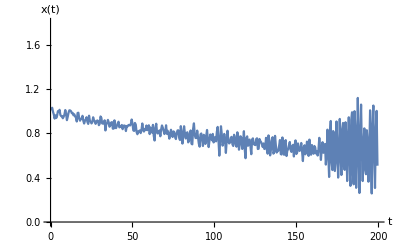

```mathematica
(* plot of x variable in time *)
plotX = ListPlot[xSeries,
Joined->True,
ImageSize->400,
LabelStyle->14,
AxesLabel->{"t","x(t)"},
PlotRange->{0,1.8},
ImagePadding->padTop]
```

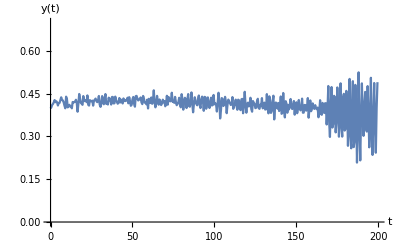

```mathematica
(* plot of y variable in time *)
plotY = ListPlot[ySeries,
Joined->True,
ImageSize->400,
LabelStyle->14,
AxesLabel->{"t","y(t)"},
PlotRange->{0,0.7},
ImagePadding->padTop]
```

## Bifurcation diagram X

### Specifications

```mathematica
(* Import data *)
rawdata=Import["bifurcation_data/cr1x.dat"];

lt=0.0075; (* line thickness *)
ls=10; (* label size *)
ps=0.03; (* point size *)
imgs=400; (* image size *)
font={FontFamily->"Helvetica",FontSize->16}; (* font format *)
plRange={{-1,0.5},{-1,1}}; (* plot range *)
(*frLabel={"μ","x"}; (* frame label *)*)
(*aRatio=2/3; (* aspect ratio *)*)

(* Colors of equilibrium lines in order as above *)
eqColors={Black,{Black,Dashing[{lt,3lt}]},Black,{Red,Dashing[{lt,3lt}]}};
```

### Info and Setup

Stability representation in .dat file:
	1 - stable node
	2 - unstable node
	3 - stable limit cycle
	4 - unstable limit cycle

```mathematica
legendLine=LineLegend[eqColors,{"Stable node","Unstable node","Stable limit cycle","Unstable limit cycle"}]
```

### Line Plot

```mathematica
(* Split up high and low points into seperate rows *)
fulldata=Join[rawdata[[;;,{1,2,4,5}]],rawdata[[;;,{1,3,4,5}]]]//DeleteDuplicates;
(* Data using t instead of a *)
abifVals=fulldata[[;;,1]]*10;
tbifVals=(abifVals-al)*tmax /(ah-al);
fulldataT=ReplacePart[Transpose[fulldata],1->tbifVals]//Transpose;
```

```mathematica
(* Stability type of point i *)
stabType=fulldataT[[;;,3]];
```

```mathematica
numPoints=Length[fulldataT];
```

```mathematica
(* Find rows where stability has changed (bif rows) *)
bifPts={1};
i=1;
While[i<numPoints,
s=stabType[[i]];
If[s==stabType[[i+1]],i=i+1,
bifPts=Append[bifPts,i+1];i=i+1]]
```

```mathematica
(* Split up fulldata into node sections *)
nodeSections=Append[
Table[fulldataT[[bifPts⟦i⟧;;bifPts⟦i+1⟧]],{i,1,Length[bifPts]-1}], (* If line join jumps to other curves, vary this *)
fulldataT⟦Last[bifPts];;⟧];

(* Ignore sections with two points (they are the result of end points *)
nodeSections=DeleteCases[DeleteCases[nodeSections,{_}],{}];
```

```mathematica
(* Adjust certain branches *)
nodeSections=Append[nodeSections,Cases[nodeSections[[7]],{_,x_,_,_}/;x<=0.75]];
nodeSections[[7]]=Cases[nodeSections[[7]],{_,x_,_,_}/; x>=0.65] ;(* had to seperate out brances for plotting purposes *)
```

```mathematica
numBranches=Length[nodeSections];
```

```mathematica
(* Stabilty of sections *)
stab=Table[nodeSections[[i,1,3]],{i,1,numBranches}];
```

```mathematica
(* Take relevant branches of node sections *)
delList={1,2,3,6};
branchesNums=Complement[Range[1,numBranches],delList]
```

{4,5,7,8}

```mathematica
(* Color vector *)
colorScheme=eqColors[[stab[[branchesNums]]]];
```

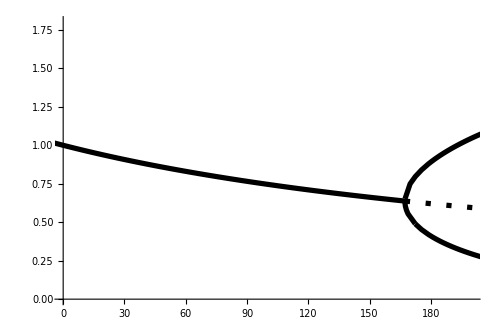

```mathematica
(* Make plot *)
bifPlotNormal=ListCurvePathPlot[Join[nodeSections[[branchesNums]]],
PlotStyle->Transpose[{colorScheme,ConstantArray[Thickness[lt],Length[colorScheme]]}],
LabelStyle->font,
InterpolationOrder->None,
PlotRange->{{0,tmax},{0,1.8}},
Axes->{True,True},
ImageSize->{500,300},
AspectRatio->2/3,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}}
]
```

### Output

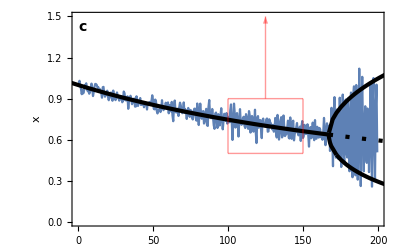

```mathematica
(* Incorporate with simulation and region of psd computation *)
lineStyle={Red,Opacity[0.4]};
sqHeight=0.2;
trajVal=0.7;

bifTrajX=Show[{plotX,bifPlotNormal},
PlotRange->{{0,tmax},{0,1.5}},
LabelStyle->14,
Frame->{{True,True},{True,True}},
AxesLabel->None,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
FrameLabel->{{"x",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
ImageSize->imgs,
Epilog->{Text[Style["c",14,Bold],Scaled[{0.035,0.93}]],
Directive[lineStyle],
Line[{{psdTime,trajVal-sqHeight},{psdTime,trajVal+sqHeight}}],
Line[{{psdTime-windowComps*dt2,trajVal-sqHeight},{psdTime-windowComps*dt2,trajVal+sqHeight}}],
Line[{{psdTime-windowComps*dt2,trajVal-sqHeight},{psdTime,trajVal-sqHeight}}],
Line[{{psdTime-windowComps*dt2,trajVal+sqHeight},{psdTime,trajVal+sqHeight}}],
Arrow[{{psdTime-windowComps*dt2/2,trajVal+sqHeight},{psdTime-windowComps*dt2/2,1.5}}]}
]
```

## Bifurcation diagram Y

### Specifications

```mathematica
(* Import data *)
rawdata=Import["bifurcation_data/cr1y.dat"];

lt=0.0075; (* line thickness *)
ls=10; (* label size *)
ps=0.03; (* point size *)
imgs=400; (* image size *)
font={FontFamily->"Helvetica",FontSize->16}; (* font format *)
plRange={{-1,0.5},{-1,1}}; (* plot range *)
(*frLabel={"μ","x"}; (* frame label *)*)
(*aRatio=2/3; (* aspect ratio *)*)

(* Colors of equilibrium lines in order as above *)
eqColors={Black,{Black,Dashing[{lt,3lt}]},Black,{Red,Dashing[{lt,3lt}]}};
```

### Info and Setup

Stability representation in .dat file:
	1 - stable node
	2 - unstable node
	3 - stable limit cycle
	4 - unstable limit cycle

```mathematica
legendLine=LineLegend[eqColors,{"Stable node","Unstable node","Stable limit cycle","Unstable limit cycle"}]
```

### Line Plot

```mathematica
(* Split up high and low points into seperate rows *)
fulldata=Join[rawdata[[;;,{1,2,4,5}]],rawdata[[;;,{1,3,4,5}]]]//DeleteDuplicates;
(* Data using t instead of mu *)
abifVals=fulldata[[;;,1]]*10;
tbifVals=(abifVals-al)*tmax /(ah-al);
fulldataT=ReplacePart[Transpose[fulldata],1->tbifVals]//Transpose;
```

```mathematica
(* Stability type of point i *)
stabType=fulldataT[[;;,3]];
```

```mathematica
numPoints=Length[fulldataT];
```

```mathematica
(* Find rows where stability has changed (bif rows) *)
bifPts={1};
i=1;
While[i<numPoints,
s=stabType[[i]];
If[s==stabType[[i+1]],i=i+1,
bifPts=Append[bifPts,i+1];i=i+1]]
```

```mathematica
(* Split up fulldata into node sections *)
nodeSections=Append[
Table[fulldataT[[bifPts⟦i⟧;;bifPts⟦i+1⟧]],{i,1,Length[bifPts]-1}], (* If line join jumps to other curves, vary this *)
fulldataT⟦Last[bifPts];;⟧];

(* Ignore sections with two points (they are the result of end points *)
nodeSections=DeleteCases[DeleteCases[nodeSections,{_}],{}];
```

```mathematica
(* Adjust certain branches *)
nodeSections=Append[nodeSections,Cases[nodeSections[[7]],{_,x_,_,_}/;x<=0.4]];
nodeSections[[7]]=Cases[nodeSections[[7]],{_,x_,_,_}/; x>=0.4] ;(* had to seperate out brances for plotting purposes *)
```

```mathematica
numBranches=Length[nodeSections];
```

```mathematica
(* Stabilty of sections *)
stab=Table[nodeSections[[i,1,3]],{i,1,numBranches}];
```

```mathematica
(* Take relevant branches of node sections *)
delList={1,2,3};
branchesNums=Complement[Range[1,numBranches],delList]
```

{4,5,6,7,8}

```mathematica
(* Color vector *)
colorScheme=eqColors[[stab[[branchesNums]]]];
```

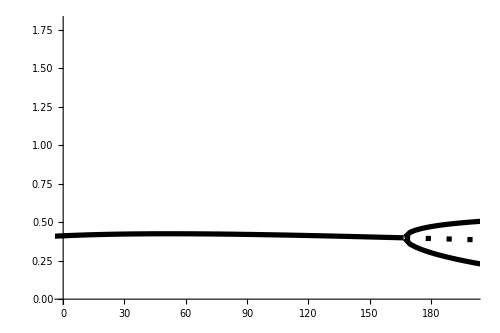

```mathematica
(* Make plot *)
bifPlotNormal=ListCurvePathPlot[Join[nodeSections[[branchesNums]]],
PlotStyle->Transpose[{colorScheme,ConstantArray[Thickness[lt],Length[colorScheme]]}],
LabelStyle->font,
InterpolationOrder->None,
PlotRange->{{0,tmax},{0,1.8}},
Axes->{True,True},
ImageSize->{500,300},
AspectRatio->2/3,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}}
]
```

### Output

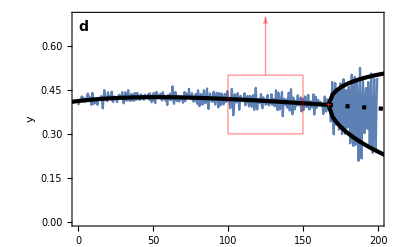

```mathematica
(* Incorporate with simulation and region of psd computation *)
lineStyle={Red,Opacity[0.4]};
sqHeight=0.1;
trajVal=0.4;

bifTrajY=Show[{plotY,bifPlotNormal},
PlotRange->{{0,tmax},{0,0.7}},
LabelStyle->14,
Frame->{{True,True},{True,True}},
AxesLabel->None,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
FrameLabel->{{"y",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
ImageSize->imgs,
Epilog->{Text[Style["d",14,Bold],Scaled[{0.035,0.93}]],
Directive[lineStyle],
Line[{{psdTime,trajVal-sqHeight},{psdTime,trajVal+sqHeight}}],
Line[{{psdTime-windowComps*dt2,trajVal-sqHeight},{psdTime-windowComps*dt2,trajVal+sqHeight}}],
Line[{{psdTime-windowComps*dt2,trajVal-sqHeight},{psdTime,trajVal-sqHeight}}],
Line[{{psdTime-windowComps*dt2,trajVal+sqHeight},{psdTime,trajVal+sqHeight}}],
Arrow[{{psdTime-windowComps*dt2/2,trajVal+sqHeight},{psdTime-windowComps*dt2/2,0.7}}]}
]
```

## Ensemble Plot